```mathematica
u[x_, t_] := (t - .5x) / (1 + (t-.5x)^2)
```

General::prng: Value of option PlotRange -> {0,0.6,Null} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

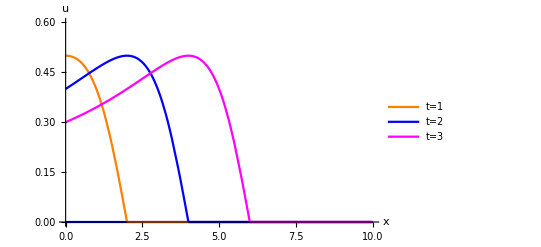

Null

```mathematica
p0 = Plot[u[x, 0] Boole[x< 0],{x, 0, 10}, PlotRange->{0, .6}, PlotStyle-> Blue, AxesLabel->{Style["x",Bold,16],Style["u",Bold,16]}];
p1 = Plot[u[x, 1] Boole[x< 2(1)],{x, 0, 10},PlotRange->{0, .6}, PlotStyle->Orange, PlotLegends->{"t=1"}];
p2 = Plot[u[x, 2] Boole[x< 2(2)],{x, 0, 10}, PlotRange->{0, .6,}, PlotStyle-> Blue, PlotLegends->{"t=2"}];
p3 = Plot[u[x, 3] Boole[x< 2(3)],{x, 0, 10}, PlotRange->{0, .6}, PlotStyle->Magenta, PlotLegends->{"t=3"}];
Show[p0, p1, p2, p3]
```

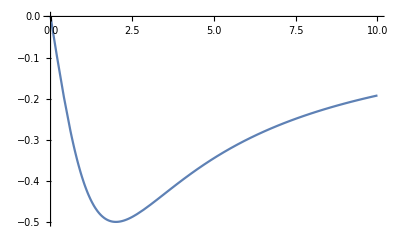

```mathematica
Plot[u[x,0], {x, 0, 10}, PlotRange->Automatic]
```